```mathematica
select[a_,b_,c_]:=If[a==1&&b==1&&c==1,1,If[a==-1&&b==-1&&c==-1,-1,0]]

endQ[b_]:={
select[b[[1]],b[[2]],b[[3]]],
select[b[[4]],b[[5]],b[[6]]],
select[b[[7]],b[[8]],b[[9]]],
select[b[[1]],b[[4]],b[[7]]],
select[b[[2]],b[[5]],b[[8]]],
select[b[[3]],b[[6]],b[[9]]],
select[b[[1]],b[[5]],b[[9]]],
select[b[[3]],b[[5]],b[[7]]]
}
```

## 対戦（人が先手）

```mathematica
Clear[bestChoice];
bestChoice[board_,x_,steps_]:=bestChoice[board,x,steps]=Module[{end=endQ@board,choice,newBoard,best},
If[MemberQ[end,1],{Null,1,steps},
If[MemberQ[end,-1],{Null,-1,steps},
If[Not@MemberQ[board,0],{Null,0,steps},
choice={Null,-x Infinity,Infinity};
Do[
If[board[[i]]==0,
newBoard=ReplacePart[board,i->x];
best=bestChoice[newBoard,-x,steps+1];
If[If[x>0,GreaterEqual,LessEqual][best[[2]],choice[[2]]],
If[Or[If[x>0,Greater,Less][best[[2]],choice[[2]]],
best[[3]]<choice[[3]]],
choice={i,best[[2]],best[[3]]}]]],
{i,1,9}];
choice]]]]
```

```mathematica
expand[board_,x_]:=Module[{end=endQ@board,newBoard,com},
If[Not@MemberQ[end,1]&&Not@MemberQ[end,-1],
Do[
If[board[[i]]==0,
newBoard=ReplacePart[board,i->x];
com=bestChoice[newBoard,-x,0][[1]];
If[com=!=Null,newBoard=ReplacePart[newBoard,com->-x]];
AppendTo[boardList,newBoard];
++p;
page[newBoard]=p;
index[board,i]=p;
AppendTo[graph,page[board]->page[newBoard]];
If[com=!=Null,expand[newBoard,x]]],
{i,1,9}]]]
```

```mathematica
p=1;
board=Table[0,{9}];
graph={};
boardList={board};
Clear[page,index];
page[board]=p;
expand[board,1];
p
```

952

### グラフ作成

```mathematica
Table[{Mod[i,3]-1,(1-Quotient[i,3])},{i,0,8}]
```

{{-1,1},{0,1},{1,1},{-1,0},{0,0},{1,0},{-1,-1},{0,-1},{1,-1}}

```mathematica
n=100;
image[pos_,board_]:=Table[{If[board[[i+1]]==1,Red,If[board[[i+1]]==-1,Blue,Gray]],Disk[pos+{(Mod[i,3]-1)/n,(1-Quotient[i,3])/n},1/n/2]},{i,0,8}]
```

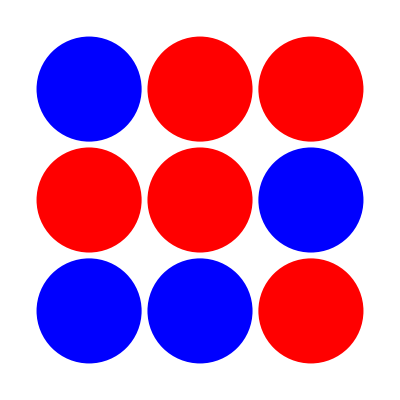

```mathematica
Graphics[image[{0,0},boardList[[100]]]]
```

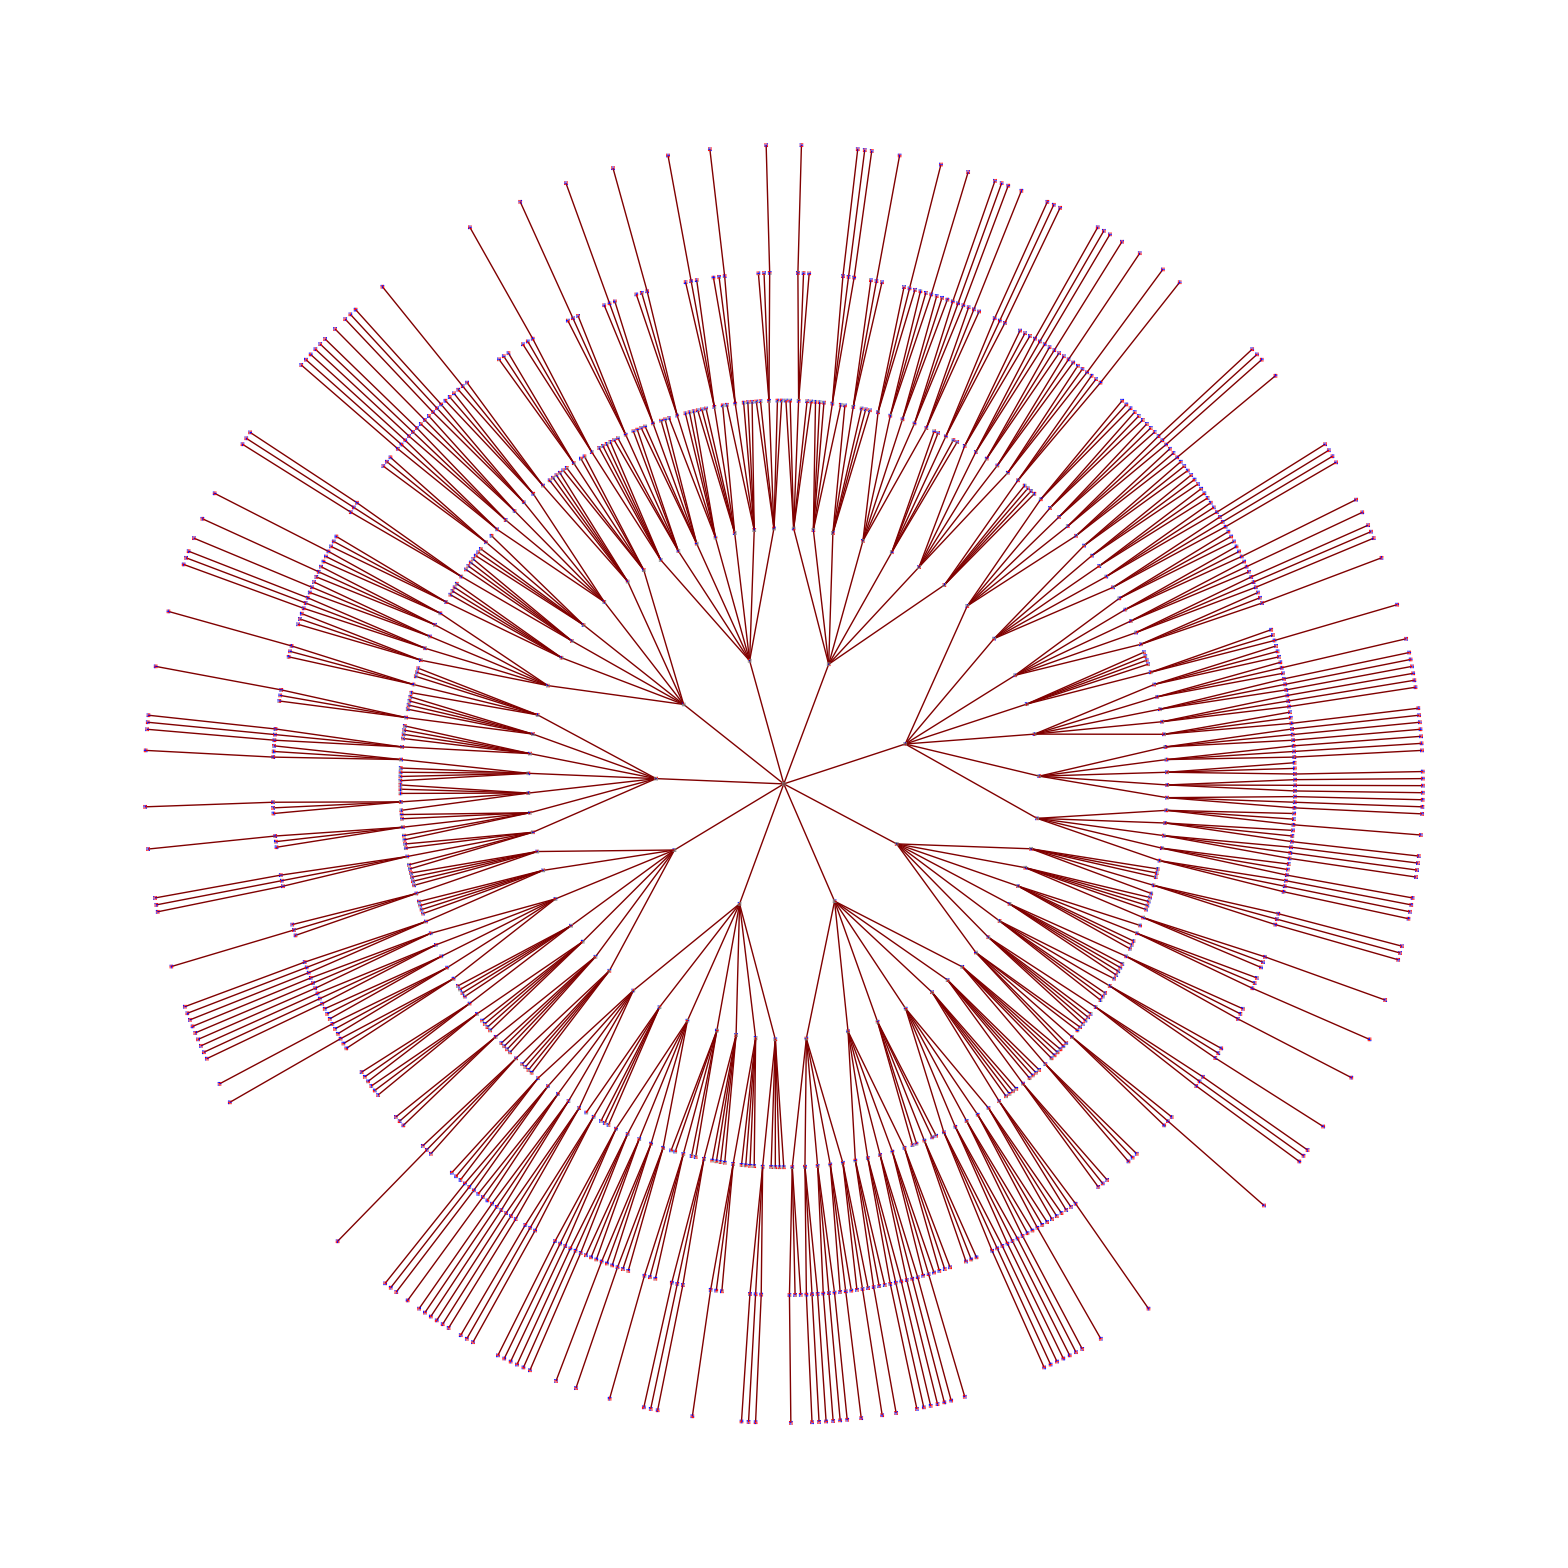

```mathematica
GraphPlot[graph,ImageSize->5000,VertexRenderingFunction->(image[#1,boardList[[ToExpression[#2]]]]&)]
```

## 対戦（COMが先手）グラフ作成

### パターン1

```mathematica
p=1;
board=Table[0,{9}];
graph={};
board[[1]]=1;
boardList={board};
Clear[page,index];
page[board]=p;
expand[board,-1];
p
```

91

### パターン2

```mathematica
p++;
board=Table[0,{9}];
board[[2]]=1;
AppendTo[boardList,board];
page[board]=p;
expand[board,-1];
p
```

224

### パターン3

```mathematica
p++;
board=Table[0,{9}];
board[[5]]=1;
AppendTo[boardList,board];
page[board]=p;
expand[board,-1];
p
```

343

### グラフ作成

```mathematica
AppendTo[graph,p+1->1];
AppendTo[graph,p+1->92];
AppendTo[graph,p+1->225];
AppendTo[boardList,Table[0,{9}]];
```

```mathematica
n=60;
image[pos_,board_]:=Table[{If[board[[i+1]]==1,Red,If[board[[i+1]]==-1,Blue,Gray]],Disk[pos+{(Mod[i,3]-1)/n,(1-Quotient[i,3])/n},1/n/2]},{i,0,8}]
```

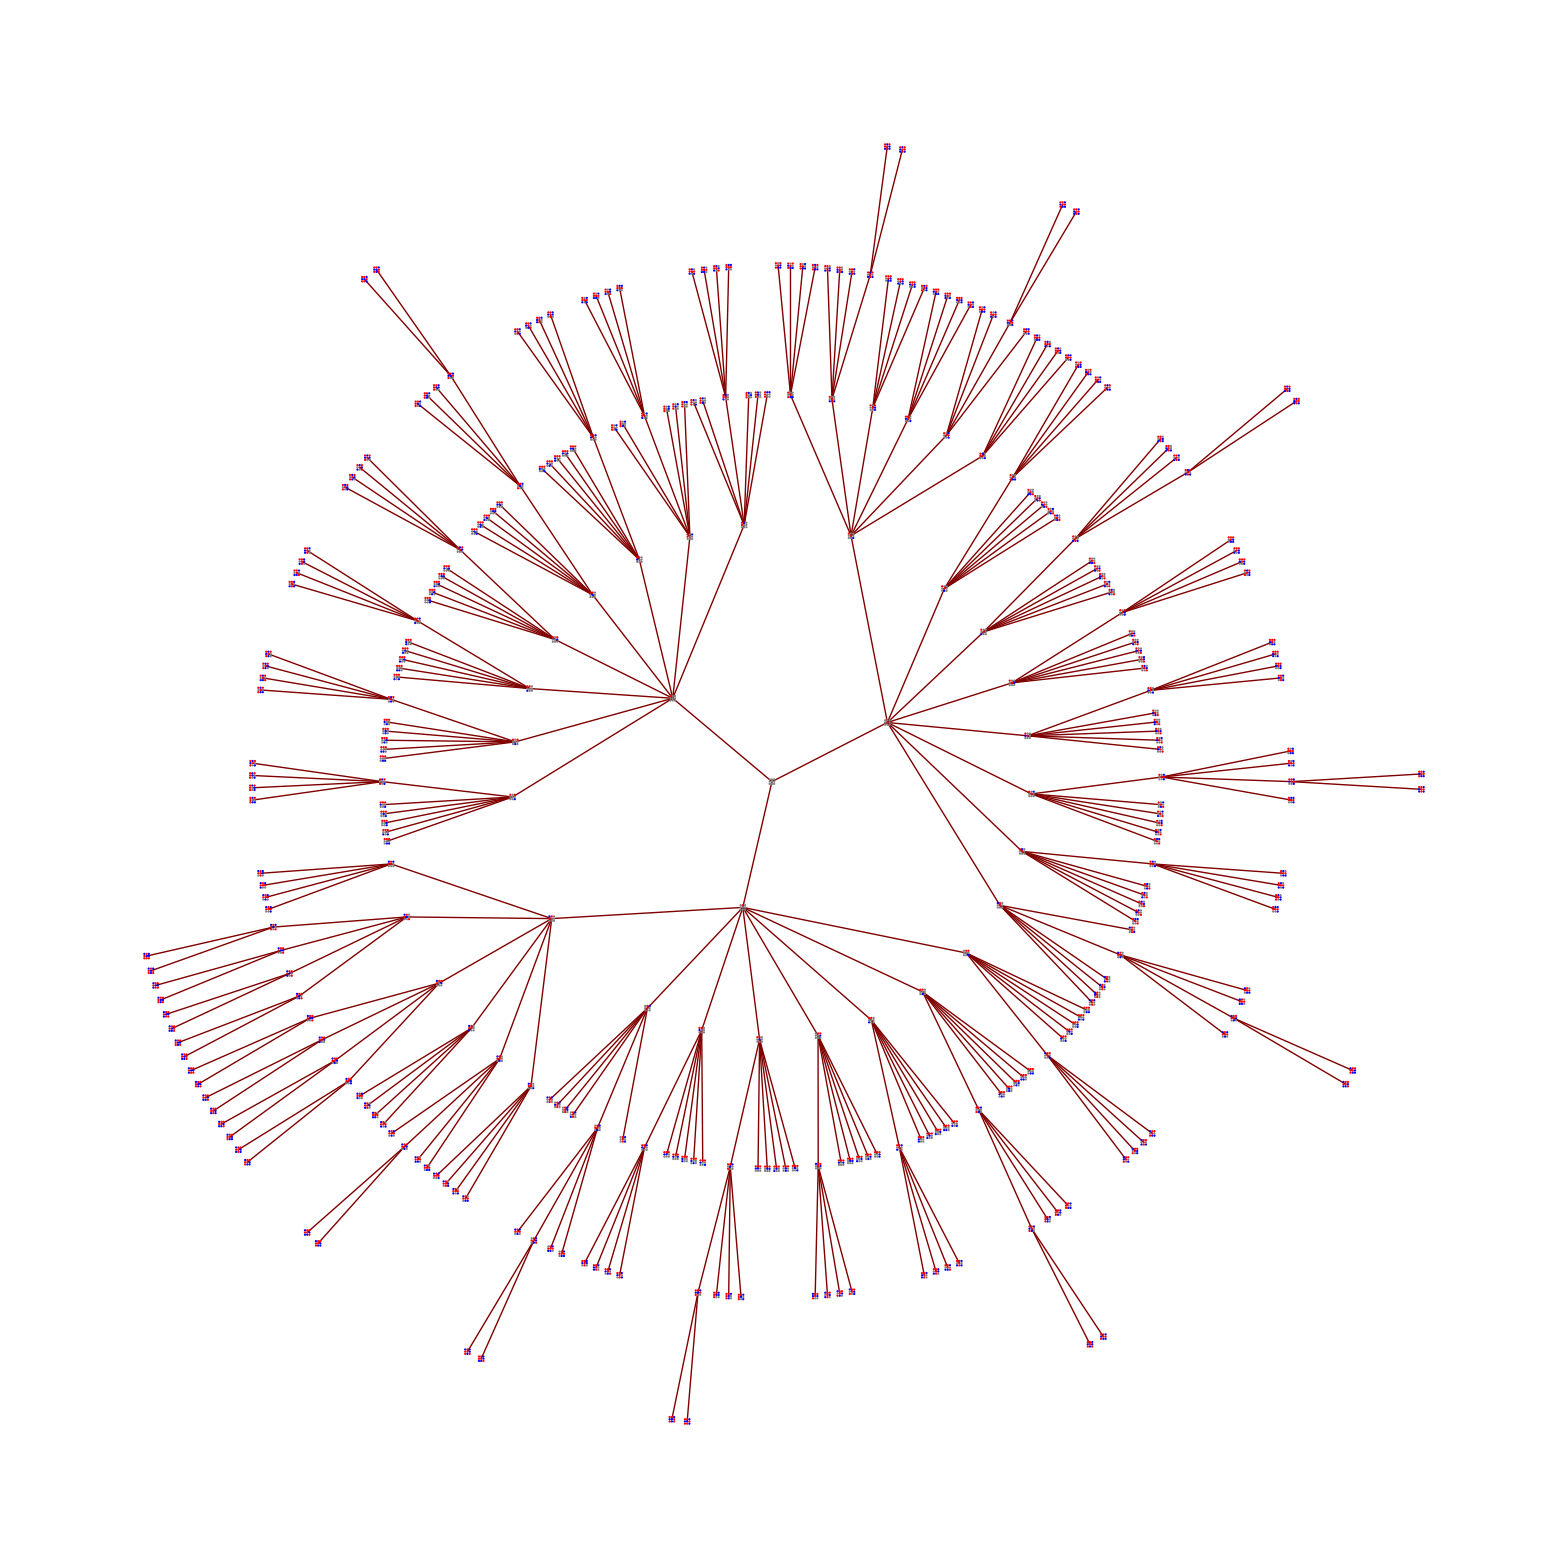

```mathematica
GraphPlot[Union[graph],ImageSize->3000,VertexRenderingFunction->(image[#1,boardList[[ToExpression[#2]]]]&)]
```